### Globals

```mathematica
$HistoryLength=0;ClearAll["Global`*"];
```

```mathematica
au=1.5*10^13;
G=6.67*10^-8;
σ = 5.67*10^-5;
Msun=2*10^33;
year=3.15*10^7;
Rsun=0.00465 au;
```

### Params

```mathematica
sizeFactor=1.0;
Bstar = 500;
Mstar=sizeFactor*Msun;
Rstar = sizeFactor*2 * Rsun;
mdot = sizeFactor * 10^-8 Msun/year;
```

### Rms

```mathematica
rmsAu=((3 Bstar^2 Rstar^6)/(2 mdot √(G Mstar)))^(2/7)/au
```

0.0504449

### Rdz

```mathematica
Tdisk[r_]:=((3 G Mstar mdot)/(8 π σ (r*au)^3)(1-√(Rstar/(r*au))))^(1/4)
diskMassFraction=0.024033;
Σ[r_]:=(diskMassFraction/0.024033*Mstar/Msun)1700* (r/r0disk)^(-3/2);
```

```mathematica
τ[r]:=1/2 Σ[r]* kr
Tc[r_]:=(Tdisk^4 3/4 τ[r])^(1/4)
```

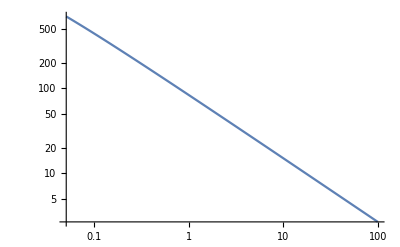

```mathematica
LogLogPlot[Tdisk[r],{r,rmsAu,100}, GridLines->{{0,0},{}}]
```